```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[Epi_,T_]:=1/(Exp[Epi/T]-1);
nbd1x[Epi_,T_]:=-1/T nb[Epi,T](nb[Epi,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
(*Epi[q_]:=√(q^2+mp2);*)
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B2thr[Epi_,mf2_,p0_,q_,T_,mu_]:=1/2 (-(0+nb[Epi[q],T])/(2 Epi[q]^3 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2))+nbd1x[Epi[q],T]/(2 Epi[q]^2 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2))-nb[Epi[q],T]/(2 Epi[q]^3 (-Eq[q,mf2]^2+(Epi[q]-mu+ⅈ p0)^2))+nbd1x[Epi[q],T]/(2 Epi[q]^2 (-Eq[q,mf2]^2+(Epi[q]-mu+ⅈ p0)^2))-nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2)^2)-(-0+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((0+nb[Epi[q],T]) (-Epi[q]-mu+ⅈ p0))/(Epi[q]^2 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2)^2)-(nb[Epi[q],T] (Epi[q]-mu+ⅈ p0))/(Epi[q]^2 (-Eq[q,mf2]^2+(Epi[q]-mu+ⅈ p0)^2)^2));
F1B2vac[Epi_,mf2_,p0_,q_,T_,mu_]:=1/2 (-1/(2 Epi[q]^3 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2))--1/(Eq[q,mf2] (-Epi[q]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((1) (-Epi[q]-mu+ⅈ p0))/(Epi[q]^2 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2)^2));
Zpsi[Epi_,mf2_,h_,p0_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(3 π^2)(NIntegrate[q^4 Re[F1B2vac[Epi,mf2,p0,q,T,mu]],{q,1,1000}]+NIntegrate[q^4 Re[F1B2thr[Epi,mf2,p0,q,T,mu]],{q,1,2000}])+1
```

```mathematica
fpidata=Transpose[Import["../../../../sigma0.dat"]];
q=Table[i,{i,1,2000,10}];
T=190;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
mu=Flatten[Table[i*5.,{i,1,80,1}]];
Length[q]
Length[sigmapi]
```

200

80

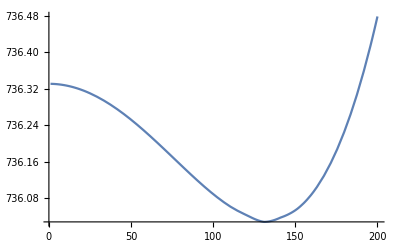

```mathematica
Plot[sigmapi[[70]][q],{q,1,200}]
```

```mathematica
T=10;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
data=Table[Zpsi[sigmapi[[i]],mf2[6.5,(fpidata[[T]][[i]])^2/2],6.5,π  T,T,mu[[i]]],{i,1,80}]
Export["./T"<>ToString[T]<>"/Zpsi.dat",data]
```

{1.20541,1.20543,1.20548,1.20554,1.20561,1.20571,1.20582,1.20595,1.2061,1.20626,1.20645,1.20665,1.20687,1.2071,1.20736,1.20763,1.20792,1.20824,1.20857,1.20892,1.20929,1.20968,1.21009,1.21052,1.21097,1.21145,1.21194,1.21246,1.213,1.21357,1.21415,1.21476,1.2154,1.21606,1.21675,1.21746,1.2182,1.21897,1.21977,1.2206,1.22145,1.22234,1.22326,1.22422,1.2252,1.22623,1.22729,1.22839,1.22953,1.23072,1.23195,1.23324,1.23459,1.23602,1.23755,1.23922,1.24111,1.24336,1.24626,1.25047,1.36234,1.34866,1.33574,1.3241,1.31363,1.30419,1.29564,1.28784,1.28071,1.27416,1.26811,1.2625,1.25729,1.25242,1.24785,1.24357,1.23952,1.2357,1.23207,1.22862}

./T10/Zpsi.dat

```mathematica
T=50;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
data=Table[Zpsi[sigmapi[[i]],mf2[6.5,(fpidata[[T]][[i]])^2/2],6.5,π  T,T,mu[[i]]],{i,1,80}]
Export["./T"<>ToString[T]<>"/Zpsi.dat",data]
```

{1.20188,1.2019,1.20193,1.20197,1.20203,1.20209,1.20217,1.20227,1.20237,1.20249,1.20262,1.20276,1.20291,1.20308,1.20326,1.20345,1.20365,1.20386,1.20409,1.20433,1.20458,1.20484,1.20512,1.20541,1.20571,1.20602,1.20634,1.20668,1.20702,1.20738,1.20775,1.20814,1.20853,1.20894,1.20936,1.20979,1.21024,1.2107,1.21117,1.21166,1.21216,1.21269,1.21323,1.21379,1.21439,1.21501,1.21567,1.21639,1.21717,1.21803,1.21902,1.22019,1.22163,1.22352,1.22621,1.23028,1.23393,1.23225,1.22819,1.22365,1.21916,1.21488,1.21085,1.20706,1.20351,1.20018,1.19704,1.19407,1.19126,1.1886,1.18606,1.18363,1.18131,1.17909,1.17694,1.17487,1.17287,1.17093,1.16904,1.1672}

./T50/Zpsi.dat

```mathematica
T=190;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
data=Table[Zpsi[sigmapi[[i]],mf2[6.5,(fpidata[[T]][[i]])^2/2],6.5,π  T,T,mu[[i]]],{i,1,80}]
Export["./T"<>ToString[T]<>"/Zpsi.dat",data]
```

{1.10644,1.10638,1.10629,1.10616,1.10599,1.10578,1.10554,1.10526,1.10495,1.10461,1.10423,1.10382,1.10338,1.10291,1.10241,1.10189,1.10134,1.10076,1.10017,1.09955,1.0989,1.09824,1.09756,1.09687,1.09615,1.09543,1.09468,1.09393,1.09316,1.09239,1.0916,1.0908,1.09,1.08919,1.08837,1.08755,1.08672,1.08589,1.08505,1.08421,1.08337,1.08253,1.08168,1.08083,1.07998,1.07913,1.07828,1.07743,1.07658,1.07573,1.07488,1.07403,1.07319,1.07234,1.07149,1.07065,1.06981,1.06897,1.06813,1.06729,1.06645,1.06562,1.06479,1.06396,1.06313,1.0623,1.06148,1.06065,1.05983,1.05901,1.0582,1.05738,1.05657,1.05576,1.05495,1.05414,1.05334,1.05254,1.05174,1.05094}

./T190/Zpsi.dat